# Choosing Best From 3 methods

```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True];
NotebookSave[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
$Path=Append[$Path,#]&/@FileNames["*",{Directory[]<>"\1DPackage"}];
```

```mathematica
<<"pyramid1d`"
<<"pyramidalStereoAll`"
<<"PixelTest`"
<<"LineTest`"
```

## read

```mathematica
read[set_,num_,reduce_,corf_]:=Module[{ia,ib,id,rgb2d,reduire,clean,io,left,right,disp,occ, frame, base,fileleft,fileright},(

base="D:\MastersMathematica\Data\Sintel";

frame="frame_"<>num<>".png";
fileleft=corf<>"_left";
fileright=corf<>"_right";
left=FileNameJoin[{base,"training",fileleft,set,frame}];
right=FileNameJoin[{base,"training",fileright,set,frame}];
disp=FileNameJoin[{base,"training","disparities",set,frame}];
occ=FileNameJoin[{base,"training","occlusions",set,frame}];

rgb2d[{r_,g_,b_}]:=r*4+g/64;
clean[img_]:=Image[ImageData[img]];
reduire[img_,1]:=img;
reduire[img_,factor_]:=ImageResize[img,ImageDimensions[img]/factor];
ia=reduire[ColorConvert[clean@Import[left],"GrayScale"],reduce];
ib=reduire[ColorConvert[clean@Import[right],"GrayScale"],reduce];
id=reduire[Image[
rgb2d[Flatten[N@ImageData[clean@Import[disp],"Byte"],{{3},{1},{2}}]]
],reduce]/reduce;
io=reduire[ColorConvert[clean@Import[occ],"GrayScale"],reduce];
read[{left,right,disp,occ},reduce]={ia,ib,id,io};

{ia,ib,id,io}
)];
```

## Test Design

```mathematica
(*Counts the amount of colors in solution*)
countColors[v_]:=Block[{count},
count=0;
ImageScan[If[Mean[#]≠0,count++]&,v];
count
]
```

```mathematica
(*Runs different tests {1,m}, {n,n}, {n,m}, {2,m+1}*)
(*Error is updated depending in the highest res level *)

testn=4;

test1[ia_,ib_,lvl_,e_,mode_]:=Block[{},(

Flatten[Table[
{stereoDepth[ia,ib,lvl,{i,lvl},e,mode],
stereoDepth[ia,ib,i,{i,i},e,mode],
stereoDepth[ia,ib,i,{1,i},e,mode],
stereoDepth[ia,ib,i+1,{2,i+1},e,mode]
}
,{i,lvl}],1]

)]
```

```mathematica
test2[ia_,ib_,{lvlmin_,lvlmax_},e_,mode_]:=Block[{},(
stereoDepth[ia,ib,lvlmax,{lvlmin,lvlmax},e,mode]
)]
```

```mathematica
(* Formats result  to show minMax in solution,disparity map, real solution, status map, Histogram, cero count and RMES *)

result1[t_,s_]:=Block[{minmaxid,flipMask,signMask,magMask,okMask,convergedMask,lst1,lst2,p,histogram,imageConverged,imageOk,imageFlip,imageSign,imageMag},(

minmaxid=MinMax[Flatten[ImageData[s]]];
(*seeStatus={"converged"->Transparent,"ok"->Transparent,"flip"->Red,"sign"->Purple,"mag"->Yellow};*)
flipMask={"converged"->Transparent,"ok"->Transparent,"flip"->Orange,"sign"->Transparent,"mag"->Transparent};
signMask={"converged"->Transparent,"ok"->Transparent,"flip"->Transparent,"sign"->Red,"mag"->Transparent};
magMask={"converged"->Transparent,"ok"->Transparent,"flip"->Transparent,"sign"->Transparent,"mag"->Purple};
okMask={"converged"->Transparent,"ok"->Pink,"flip"->Transparent,"sign"->Transparent,"mag"->Transparent};
convergedMask={"converged"->Green,"ok"->Transparent,"flip"->Transparent,"sign"->Transparent,"mag"->Transparent};

Table[
lst1=Flatten[-result[[All,All,1]]];
lst2=Flatten[ImageData[s]];

p=Flatten[Position[Flatten[result[[All,All,2]]],#]&/@{"sign","mag","flip","ok"},1];
lst1=Delete[lst1,p];
lst2=Delete[lst2,p];

histogram=Histogram[Clip[#&/@{lst1,lst2},{-1,50}],{0.1}];
histogram2=Histogram[Clip[#&/@{Flatten[-result[[All,All,1]]],Flatten[ImageData[s]]},{-1,50}],{0.1}];

imageConverged=Image[result[[All,All,2]]/.convergedMask];
imageOk=Image[result[[All,All,2]]/.okMask];
imageFlip=Image[result[[All,All,2]]/.flipMask];
imageSign=Image[result[[All,All,2]]/.signMask];
imageMag=Image[result[[All,All,2]]/.magMask];

{Image[-result[[All,All,1]]]/(minmaxid[[2]]),
s/(minmaxid[[2]]),
Grid[{{imageConverged},{countColors[imageConverged]}}],
Grid[{{imageOk},{countColors[imageOk]}}],
Grid[{{imageFlip},{countColors[imageFlip]}}],
Grid[{{imageSign},{countColors[imageSign]}}],
Grid[{{imageMag},{countColors[imageMag]}}],
countColors[imageFlip]+countColors[imageSign]+countColors[imageMag],
Show[histogram],
N@Sqrt[Mean[Power[lst1-lst2,2]]],
Show[histogram2],
N@Sqrt[Mean[Power[Flatten[-result[[All,All,1]]]-Flatten[ImageData[s]],2]]]
}

,{result,t}]

)]
```

## Data 1

```mathematica
d=1;

(* downscaling *)
r=2;
{ia,ib,id,io}=read["bamboo_1","0001",r,"clean"]

MinMax[id]

(* a reduction of 6 is {173,73} *)
(*{ia,ib,id,io}=ImageCrop[#,{173,73}]&/@{ia,ib,id,io}*)

(* {1,44},{1,102} arbitrary size to make the method faster *)
nx=150/r;
ny=300/r;
{ia,ib,id,io}=ImageTake[#,{ny,ny+44},{nx,nx+102}]&/@{ia,ib,id,io}
ImageDimensions[#]&/@{ia,ib,id,io}
ic=move[ia,-7]
max=MinMax[Flatten[ImageData[id]]][[2]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{0.136895,38.6009}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{{103,45},{103,45},{103,45},{103,45}}

-Graphics-

12.5952

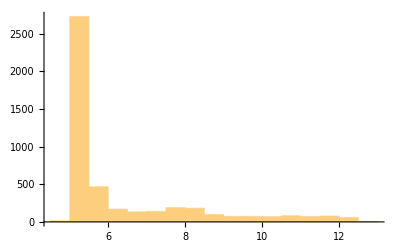

{4.70419,12.5952}

```mathematica
Histogram[Flatten[ImageData[id]]]
minmaxid=MinMax[Flatten[ImageData[id]]]
```

## Little Tests

Cases where we can find issues or cases where it’s working

#### Little Test 1

```mathematica
(* data we work with *)
{ia,ic}
```

{-Graphics-,-Graphics-}

```mathematica
(*"OverConstrained"*)
(*"Constrained"*)
mode="SemiConstrained";
e=0.02;
lvlmin=3;
lvlmax=5;
```

```mathematica
(* Check solution *)
Image[-test2[ia,ic,{lvlmin,lvlmax},e,mode][[All,All,1]]]/max
```

-Graphics-

```mathematica
row=14;
pyrfia=pyrFuncGen[ImageData[ia][[row]], lvlmax];
pyrfib=pyrFuncGen[ImageData[ic][[row]],lvlmax];

pyrfi=Flatten[{pyrfia,pyrfib},{{2},{1},{3}}];
```

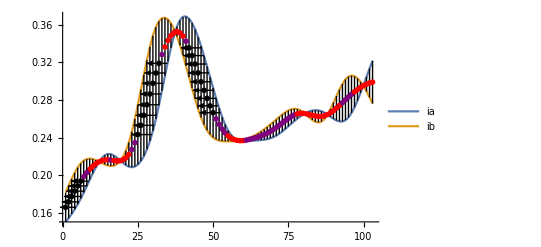

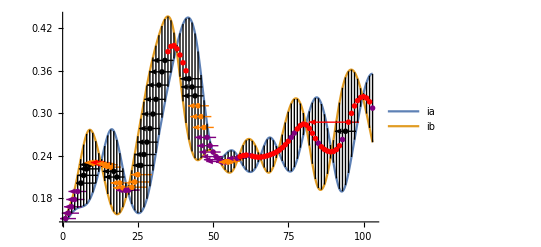

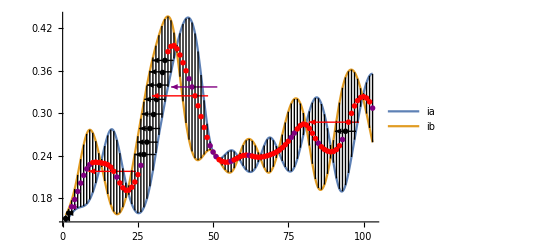

```mathematica
(*lineTest[Range[30,35],{lvlmin,lvlmax},pyrfi,e,mode]*)

lineTest[Range[ImageDimensions[ia][[1]]],{lvlmin+1,lvlmin+1},pyrfi,e,mode]
lineTest[Range[ImageDimensions[ia][[1]]],{lvlmin,lvlmax},pyrfi,e,mode]
lineTest[Range[ImageDimensions[ia][[1]]],{lvlmin,lvlmin},pyrfi,e,mode]
```

#### Little Test 2

```mathematica
(* data we work with *)
{ia,ic}
```

{-Graphics-,-Graphics-}

```mathematica
(*"OverConstrained"*)
(*"Constrained"*)
mode="SemiConstrained";
e=0.02;
lvlmin=2;
lvlmax=5;
```

```mathematica
(* Check solution *)
Image[-test2[ia,ic,{lvlmin,lvlmax},e,mode][[All,All,1]]]/(max+10)
id/(max+10)
```

-Graphics-

-Graphics-

```mathematica
row=16;
pyrfia=pyrFuncGen[ImageData[ia][[row]], lvlmax];
pyrfib=pyrFuncGen[ImageData[ic][[row]],lvlmax];

pyrfi=Flatten[{pyrfia,pyrfib},{{2},{1},{3}}];
```

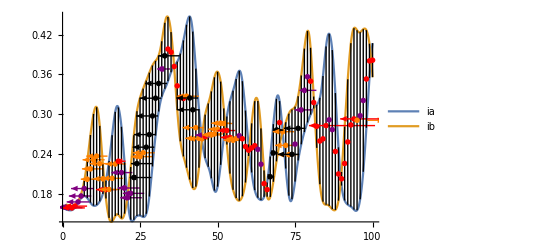

```mathematica
lineTest[Range[1,100],{lvlmin,lvlmax},pyrfi,e,mode]
```

```mathematica
e*2^(-lvlmin+1)
ListAnimate[pixelTest[9,40,{lvlmin,lvlmax},pyrfi,e,mode]]
```

0.01

#### Little Test 3

```mathematica
(* data we work with *)
{ia,ic=move[ib,4]}
```

{-Graphics-,-Graphics-}

```mathematica
(*"OverConstrained"*)
(*"Constrained"*)
mode="OverConstrained";
e=0.02;
lvlmin=3;
lvlmax=5;
```

```mathematica
(* Check solution *)
Image[-test2[ia,ic,{lvlmin,lvlmax},e,mode][[All,All,1]]+4]/max
id/max
```

-Graphics-

-Graphics-

```mathematica
row=16;
pyrfia=pyrFuncGen[ImageData[ia][[row]], lvlmax];
pyrfib=pyrFuncGen[ImageData[ic][[row]],lvlmax];

pyrfi=Flatten[{pyrfia,pyrfib},{{2},{1},{3}}];
```

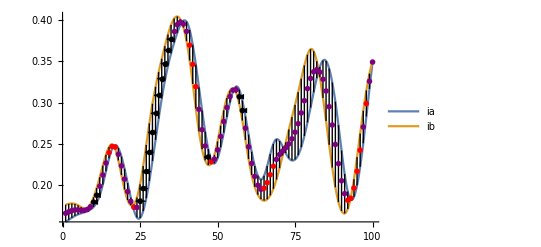

```mathematica
lineTest[Range[1,100],{lvlmin,lvlmax},pyrfi,e,mode]
```

```mathematica
e*2^(-lvlmin+1)
ListAnimate[pixelTest[9,40,{lvlmin,lvlmax},pyrfi,e,mode]]
```

0.005